```mathematica
SetDirectory[NotebookDirectory[] <> ".."];
```

```mathematica
Load[name_] := Module[{f=Import[name,{"Real64"}]},
G = f⟦1⟧;
n = IntegerPart[f⟦2⟧];
f = Drop[f, 2];
frames = Transpose[ArrayReshape[f, {Length[f] / (n*4+3), n*4 + 3}]];
time = frames⟦1⟧;
dt = (time⟦#1⟧ - time⟦#1 - 1⟧)&/@Range[2, Length[time]];
potential = frames⟦2⟧;
kinetic = frames⟦3⟧;
bodies = Drop[Drop[frames, 3],4;;;;4];
frameN = Length[bodies⟦1⟧];
{Transpose[#1]&/@ArrayReshape[bodies, {n, 3, frameN}], time, {potential, kinetic}, dt}
];
```

```mathematica
file = Load["test6.bin"];
```

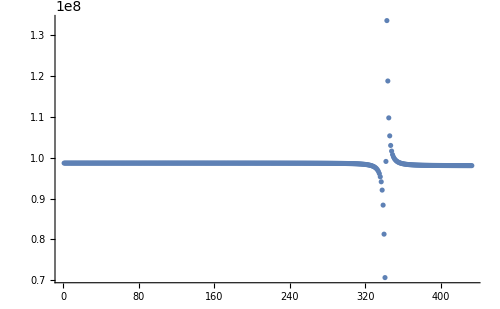

```mathematica
ListPlot[{file⟦3, 2⟧ + file⟦3, 1⟧}, ImageSize->500, PlotRange->All]
```